## Golden Ratio

```mathematica
gr=(1+Sqrt[5])/2
```

1/2 (1+√5)

```mathematica
N[gr,10]
```

1.618033989

```mathematica
sols=Solve[3 Sqrt[3] s^2 /2 == L^2,s]
```

{{s→-(√2 L)/3^(3/4)},{s→(√2 L)/3^(3/4)}}

```mathematica
sols[[2]]//N
```

{s→0.620403 L}

```mathematica
sol1=s/.sols[[2]]/.{L->1}
```

(√2)/3^(3/4)

```mathematica
N[1/sol1,10]
```

1.611854898

```mathematica
1/sol1
```

3^(3/4)/(√2)

```mathematica
(N[1/sol1,10]-N[gr,10])/(N[gr,10])
```

-0.003818888

```mathematica
1/.62
```

1.6129

```mathematica
.62*500
```

310.

```mathematica
250/.62
```

403.226

```mathematica
Sqrt[2]/(3^.75)
```

0.620403

```mathematica
(3^.75)/Sqrt[2]
```

1.61185

```mathematica
getEqui[s_]:=Module[{h},
h=s*Sqrt[3]/2;
{{0,0},{h,-s/2},{h,s/2}}];
```

```mathematica
rot[p_,th_]:=Module[{c=Cos@th,s=Sin@th,m},
m={{c,-s},{s,c}};
m.p];
```

```mathematica
rot[{1,0},.1]
```

{0.995004,0.0998334}

```mathematica
Clear@drawHex;
drawHex[s_,lrect0_]:=Module[{e1,hex,hex2,lrect},
e1=getEqui[s];
lrect=s/sol1;
hex=Table[rot[e1[[3]],th],{th,0,2π-π/3,π/3}];
hex2=2#&/@hex;
Graphics[{FaceForm@None,PointSize@Large,Black,Point@{0,0},
{EdgeForm@{Blue,Thick},Polygon@hex,EdgeForm@{Blue,Dashed},Polygon@hex2,Rectangle[{-lrect,-lrect},{lrect,lrect}]},
{EdgeForm@{Blue,Thick},Rectangle[{-lrect/2,-lrect/2},{lrect/2,lrect/2}]},
{EdgeForm@{Red,Thick},Rectangle[{-lrect0/2,-lrect0/2},{lrect0/2,lrect0/2}]}
},ImageSize->800]]
```

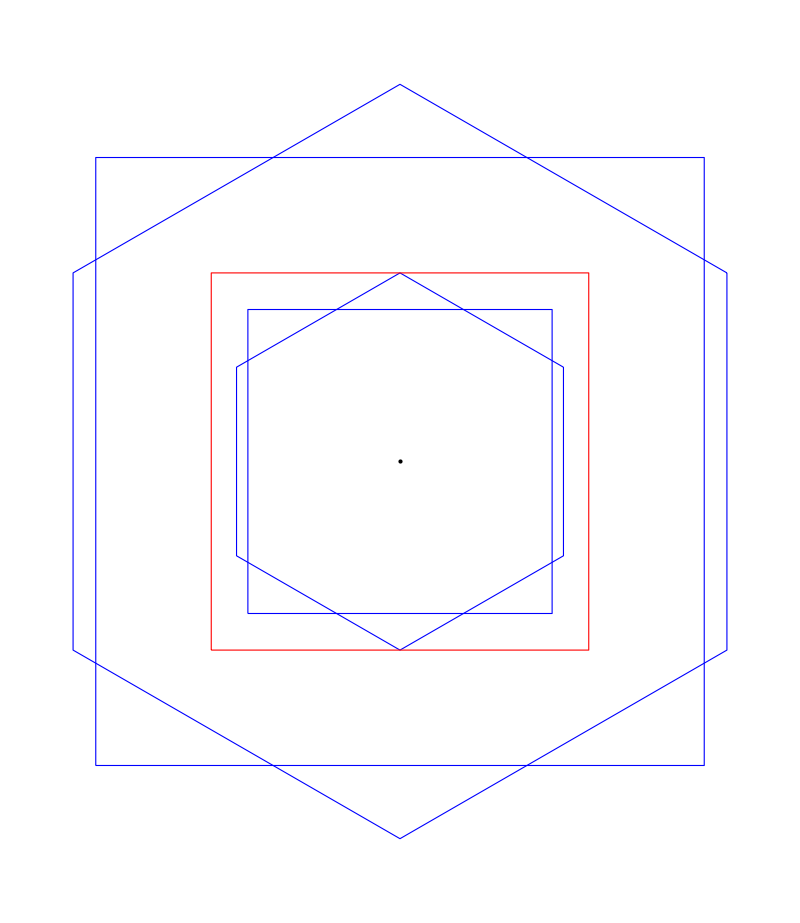

```mathematica
drawHex[250,500]
```